```mathematica
ClearAll["Global`*"]
```

## Step response

### TF function

```mathematica
k = 10;
maxt = 4;
TFstep=Simplify[OutputResponse[kTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
```

### Sizes

#### Common

```mathematica
arrowsHeads=Arrowheads[{-.035,.035}];
sizeText[text_]:=Style[text, 18,FontSlant->Italic,FontFamily->"Times New Roman"];
```

#### Vertical size

```mathematica
verSizeText=Text[
sizeText["k"],
{
-0.05,
TFstableValue
}
];
```

### Plot

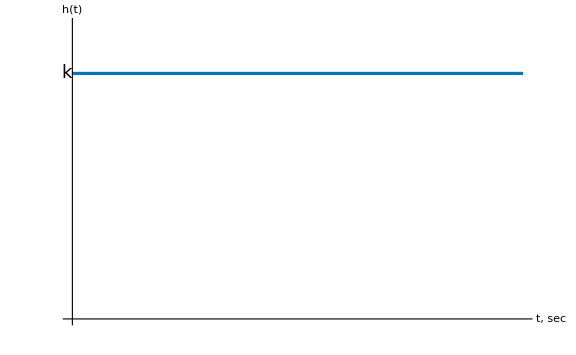

```mathematica
tickXStep = 1/2;
tickYStep = 1;
stepRespPic=Plot[{TFstep},{t, 0, maxt },
AxesStyle->Directive[Black, FontSize->9],
AxesLabel->{sizeText["t, sec"], sizeText["h(t)"]},
GridLines->None,
PlotStyle->{{RGBColor["#0077b5"],Thickness[0.004]},{Black,dashingStyle}},
PlotRange->{{0,maxt },{0,TFstableValue*1.2}},
PlotRangeClipping->False,
ImageSize->Large,
Ticks->{(#&@Array[{tickXStep #,}&,100]),(#&@Array[{tickYStep #,}&,100])},
Epilog->{
{verSizeText}
}
]
```

```mathematica
Export["step.png",stepRespPic,ImageResolution->900];
```